## Goal

Given any input state, classify it into:

- dies out
- contains multiple solutions
- periodic without shift
- periodic with shift s
- aperiodic (e.g. glider gun)

The DetectPeriod[list] function, when given an initial state, returns an association with the period, canonical representation (i.e. smallest reachable state that gives that same solution), and shift.

## Implementation

### Helper Functions

```mathematica
On[Assert];
```

```mathematica
CloseKernels[];
LaunchKernels[];
```

#### Rule Analysis

```mathematica
PointApplyRule[rule_,init_]:=CellularAutomaton[rule, init, 1][[2,(Length[init]+1)/2]]
```

```mathematica
AnalyzeRule[{n_, {k_, 1}, r_}]:=AnalyzeRule[{n, {k, 1}, r}]=Module[{rule={n, {k, 1}, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[Range[k]-1, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_, r_}]:=AnalyzeRule[{n, k, r}]=Module[{rule={n,k, r},minimumtolerablegap=2r+1},
While[AllTrue[Tuples[{0, 1}, 2r+2-minimumtolerablegap], PointApplyRule[rule, PadLeft[#, 2r+1]]==0&], minimumtolerablegap--];
<|"Rule"->rule, "Colors"->k, "Totalistic"->True, "Radius"->r, "MinimumTolerableGap"->minimumtolerablegap|>
]
AnalyzeRule[{n_, k_}]:=AnalyzeRule[{n, k, 1}]
AnalyzeRule[{n_}]:=AnalyzeRule[{n, 2}]
AnalyzeRule[n_]:=AnalyzeRule[{n}]

Timing[AnalyzeRule[{20, {2, 1}, 2}]]
AnalyzeRule[{2, {2, 1}, 2}]
AnalyzeRule[{32, {2, 1}, 2}]
AnalyzeRule[30]
RepeatedTiming[AnalyzeRule[{20, {2, 1}, 2}]]
```

{0.001726,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→4|>}

<|Rule→{2,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→5|>

<|Rule→{32,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→1|>

<|Rule→{30,2,1},Colors→2,Totalistic→True,Radius→1,MinimumTolerableGap→3|>

{1.12878×10^-7,<|Rule→{20,{2,1},2},Colors→2,Totalistic→True,Radius→2,MinimumTolerableGap→4|>}

#### General

```mathematica
AllZeros=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 1]], Module[{i=Length[list]}, While[i>0&&list[[i]]==0, i--;]; i==0]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[AllZeros[{0, 0, 0, 0, 1, 0}]]
RepeatedTiming[Max[{0, 0, 0, 0, 1, 0}]==0]
```

{2.43313×10^-7,False}

{1.98436×10^-7,False}

```mathematica
StripZeros=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list]},
While[list[[i]]==0&&i<j, i++];
 If[i<j,While[list[[j]]==0, j--]]; 
If[i==j,Table[0, 0],list[[i;;j]]]
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];

RepeatedTiming[StripZeros[RandomInteger[{0, 1}, 1000]]]//First
StripZeros[{0, 0, 0, 0,0}]
StripZeros[{0, 1, 0, 1,0}]
```

1.71387×10^-6

{}

{1,0,1}

```mathematica
MaxGapLength=FunctionCompile[Function[Typed[list, "PackedArray"::["MachineInteger", 1]],Module[
{currentlen=0, maxlen=0},
Do[currentlen=If[i==0, currentlen+1,0]; 
maxlen=Max[maxlen, currentlen];, {i,list}];
maxlen
]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
RepeatedTiming[MaxGapLength[RandomInteger[{0, 1}, 1000]]]
```

{4.95808×10^-6,9}

```mathematica
Clear[FindRepeatDeterministic];

FindRepeatDeterministicIndexCompiled=FunctionCompile[Function[Typed[list, "ListVector"::["PackedArray"::["MachineInteger", 1]]],
Module[{i=Length[list]-1, last=list[[-1]]}, While[i>0&&list[[i]]!=last, i--]; i+1]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3}];
FindRepeatDeterministic[list_List]:=list[[FindRepeatDeterministicIndexCompiled[list];;]]

RepeatedTiming[FindRepeatDeterministic[]]//First

FindRepeatDeterministicIndexByStripZerosCompiled=FunctionCompile[Function[Typed[list,"PackedArray"::["MachineInteger", 2]],
With[{StripZeros=Function[Typed[list2, "PackedArray"::["MachineInteger", 1]],Module[
{i=1, j=Length[list2]},
While[list2[[i]]==0&&i<j, i++];
 If[i<j,While[list2[[j]]==0, j--]]; 
If[i==j,Table[0, 0],list2[[i;;j]]]]
]},Module[{i=Length[list]-1, last=StripZeros[list[[-1]]]},
 While[i>0&&StripZeros[list[[i]]]!=last, i--];  If[i==0, 0,i+1]
]]], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3}];

FindRepeatDeterministicByStripZeros[list_List]:=StripZeros/@list[[FindRepeatDeterministicIndexByStripZerosCompiled[list];;]]

RepeatedTiming[FindRepeatDeterministicByStripZeros[]]//First
RepeatedTiming[FindRepeatDeterministic[StripZeros/@]]//First
Assert[FindRepeatDeterministicByStripZeros[]==FindRepeatDeterministic[StripZeros/@]]
```

3.76125×10^-6

0.0000709291

0.00261142

```mathematica
DedupSame[associations_, parameter_:"Canonical"]:=Union[associations,SameTest->(#1[parameter]==#2[parameter]&)]
```

#### DetectPeriod Subroutines

```mathematica
RunCA[rule_, init_List, steps_]:=CellularAutomaton[rule, {init, 0}, steps]
RunCA[rule_, init_Integer, steps_]:=RunCA[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], steps]

code20rule={20, {2, 1}, 2};
RunCode20[init_, steps_]:=RunCA[code20rule, init, steps]

code1329rule={1329,{3,1},1};
RunCode1329[init_, steps_]:=RunCA[code1329rule, init, steps]
```

```mathematica
Clear[SplitSeparateSolutions];
SplitSeparateSolutions[carun_, mtg_]:=Module[{mask, mc, colors, carunpadded},
carunpadded=PadLeft[carun, {Length[carun], Length[carun[[-1]]]+mtg}];
mask=Sum[carunpadded[[All,i;;(i-mtg-1)]], {i, mtg}];
mc=Last[MorphologicalComponents[Image[mask], CornerNeighbors->False]];
colors=Union[mc];
Select[Table[StripZeros[(1-Unitize[c-mc[[2;;]]])*carun[[-1]]], {c, colors}], Not@*AllZeros]
]

SplitSeparateSolutions[RunCode20[IntegerDigits[233 + 2^14 * 151, 2], 100], 4]
SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]
First@RepeatedTiming[SplitSeparateSolutions[RunCode20[IntegerDigits[12555286547204781505564672, 2], 100], 4]]
```

{{1,1,1,0,1,0,0,1},{1,0,0,1,0,1,1,1}}

{{1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,1,1,1,1}}

0.00176084

#### Visualization

```mathematica
Clear[AArrayPlot];
AArrayPlot[rule_, init_List, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule, init, steps], {ops}]
AArrayPlot[rule_, init_Integer, args___]:=AArrayPlot[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], args]

AArrayPlot[code20rule, 189, ColorRules->"Colors"]
```

-Graphics-

```mathematica
Clear[VisualizeDetectPeriod];
Clear[MultiVisualizeDetectPeriod];
VisualizeDetectPeriod[rule_, init_, stepsog_:None, ops:OptionsPattern[ArrayPlot]]:=Module[{results, steps},
results=DetectPeriod[rule, init];
steps=If[stepsog===None, Min[1000, Max[results[[All, "MaxSteps"]], 0]], stepsog];

Row[{
Labeled[AArrayPlot[rule, init, steps, {ops}], ClickToCopy["Orig", results]],
Row[
Labeled[
AArrayPlot[rule,#Canonical, 5+(3*#Period/.(0->2*steps)),{Mesh->#Period!=0,ops}],ClickToCopy[
#Period/.(0->"None"), #Canonical]]&
/@DedupSame[results]
]
}]
]
MultiVisualizeDetectPeriod[rule_, inits_, args___]:=Column[ParallelTable[VisualizeDetectPeriod[rule, init, args], {init, inits}]]
```

### Detect Period

```mathematica
SetDebug[bool_]:=(DEBUG=bool; Clear[PrintIf];PrintIf=If[DEBUG, Print, None&];)
SetDebug[False]
```

```mathematica
Clear[DetectPeriod];
Clear[DetectPeriodSub];

DetectPeriod[rule_, n_Integer, args___]:=DetectPeriod[rule, IntegerDigits[n, AnalyzeRule[rule]["Colors"]], args]
DetectPeriod[rule_, list_List, steps_:200, maxdepth_:20]:=With[{ra=AnalyzeRule[rule]}, {res=DetectPeriodSub[ra, list, steps, maxdepth]},Join[<|"Rule"->rule,"Canonical"->FromDigits[list, ra["Colors"]], "Original"->FromDigits[list, ra["Colors"]], "IsGliderGun"->False, "MaxDepth"->maxdepth-#LowestDepth, "MaxSteps"->steps*(2^(1+maxdepth-#LowestDepth)-1)|>, #]&/@res];

DetectPeriodSub[ra_, list_, steps_, ogmaxdepth_]:=Module[
{carun, frd, separatesolutions, period, canonical, shift, maxdepth},
maxdepth=ogmaxdepth;

Assert[maxdepth>=0];

carun=RunCA[ra["Rule"], list, steps];

(* If it dies, return *);
If[AllZeros[carun[[-1]]], Return[{}]];

(* Detect Periodicity *)
frd=FindRepeatDeterministicByStripZeros[carun];

If[ByteCount[carun]>8000000, maxdepth=Min[maxdepth, 2]];

If[maxdepth<=1,If[Length[frd]==0,
Return[{<|"Period"->0, "IsGliderGun"->True, "LowestDepth"->maxdepth|>}],
Return[{<|"Period"->Length[frd],"Canonical"->Min[Min[FromDigits[#,ra["Colors"]]&/@frd], Min[FromDigits[Reverse[#],ra["Colors"]]&/@frd]], "IsUnfinished"->True, "LowestDepth"->maxdepth|>}];
]];

(* If unfinished and probably unseparated, recurse with more steps *);
If[Length[frd]==0, 
Return[If[MaxGapLength[carun[[-1]]]>15,
separatesolutions=SplitSeparateSolutions[carun, ra["MinimumTolerableGap"]];
Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
],
DetectPeriodSub[ra, carun[[-1]], 2 * steps, maxdepth - 1]
]]
];


(* Otherwise, run again for pure periodicity *)
carun=RunCA[ra["Rule"], carun[[-1]], steps];

(* If it's multiperiodic, split solutions *);
separatesolutions=SplitSeparateSolutions[carun[[-Length[frd];;]], ra["MinimumTolerableGap"]];
(*separatesolutions= SortBy[separatesolutions,First[FirstPosition[#, 1, 0]]&] *);


(* Recurse on each subsolution, if they exist *);
If[Length[separatesolutions]>1,
Return[Join@@Table[
DetectPeriodSub[ra, subsolution, steps, maxdepth-1],
 {subsolution, separatesolutions}
]]
];

(* Return single-solution period *);
period=Length[frd];
canonical=Min[Min[FromDigits[#,ra["Colors"]]&/@frd], Min[FromDigits[Reverse[#],ra["Colors"]]&/@frd]];
carun=RunCA[ra["Rule"],IntegerDigits[canonical, ra["Colors"]], period];
shift=Log[ra["Colors"],FromDigits[First[carun], ra["Colors"]]/FromDigits[Last[carun], ra["Colors"]]];


Return[{<|"Period"->period,"Canonical"->canonical, "Shift"->shift, "LowestDepth"->maxdepth|>}];

]
```

```mathematica
With[{r=RandomInteger[1, 1000]},
Print[EchoTiming[DetectPeriod[code20rule,r]][[All, {"Canonical", "Period"}]]];VisualizeDetectPeriod[code20rule, r, ImageSize->{300, Automatic}]
]
```

0.017961

{<|Canonical→189,Period→1|>,<|Canonical→189,Period→1|>,<|Canonical→189,Period→1|>,<|Canonical→151,Period→2|>}

-Graphics--Graphics--Graphics-

```mathematica
RepeatedTiming[DetectPeriod[code20rule, RandomInteger[1, 100]];, 3]
```

{0.000836227,Null}

## Unit Tests

```mathematica
DetectPeriodTests[testInputs_, printPassing_:True]:=(Do[
Module[{rule, init, eval, err, d, timing, res},
If[i===Null, Continue[]];

rule=i[[1]]; init=i[[2]]; eval=i[[3]];
timing=First[AbsoluteTiming[err=Quiet@Check[d=DetectPeriod[rule, init]; res=eval[d]; False, True]]]; 

avgTiming=((passedTests+failedTests)*avgTiming+timing)/(passedTests+failedTests+1);
AppendTo[allTimings, timing];
If[err, AppendTo[badTestInputs, {rule, init, eval, "Errored"}];Break[]];

If[timing>2 avgTiming&&printPassing, AppendTo[badTestInputs, {rule, init, eval, "Took Too long"}]];

If[res,
passedTests++;
If[printPassing,Print["Passed: ", VisualizeDetectPeriod[rule, init]]];,
failedTests++;
Print["Failed: ", VisualizeDetectPeriod[rule, init, 100]];
AppendTo[badTestInputs, {rule, init, eval, "Failed Test"}]
];
], {i, testInputs}];

Echo["- - - - - Bad Test Cases - - - - -"];

Do[Module[{rule, init, eval, reason},
rule=i[[1]]; init=i[[2]]; eval=i[[3]]; reason=i[[4]];
Print[reason, ": ", VisualizeDetectPeriod[rule, init, 100, Mesh->True, ImageSize->{Automatic, 200}]]
], {i, badTestInputs}];

Print["Passed ", passedTests,"/", passedTests+failedTests, " (", N[100 passedTests/(passedTests+failedTests)],"%), Time Taken (Min/Med/Mean/Max): (",Min[allTimings], "/", Median[allTimings], "/", Mean[allTimings], "/", Max[allTimings], ")", Histogram[allTimings, 100,  ImageSize->Small]]
)
```

#### Main Tests

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics--Graphics-

Passed: -Graphics--Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Failed: -Graphics--Graphics-

Passed: -Graphics--Graphics-

Failed: -Graphics--Graphics-

Failed: -Graphics--Graphics-

Failed: -Graphics--Graphics-

Failed: -Graphics--Graphics-

Passed: -Graphics--Graphics--Graphics-

- - - - - Bad Test Cases - - - - -

Took Too long: -Graphics--Graphics-

Failed Test: -Graphics--Graphics-

Failed Test: -Graphics--Graphics-

Failed Test: -Graphics--Graphics-

Failed Test: -Graphics--Graphics-

Failed Test: -Graphics--Graphics-

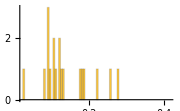
Passed 15/20 (75.%), Time Taken (Min/Med/Mean/Max): (0.027509/0.121238/0.159355/0.5726)-Graphics-

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};

testInputs={
{code20rule, 189, #[[1, "Period"]]==1&&#[[1, "Canonical"]]==189&},
{code20rule, 151, #[[1, "Period"]]==2&},
{code20rule, 187, #[[1, "Period"]]==9&},

{code20rule, 1663707641399530118980411815482221, Length[#]==2&&Length[Union[#]]==1&},
{code20rule, 229131364, Length[#]==2&&Length[Union[#]]==1&},

{code20rule, 10404475, Length[#]==2&&Length[Union[#]]==1&},
{code20rule, 24511099, Length[#]==2&&Length[Union[#]]==2&},
{code20rule, 55515189812230754905562323925615995497545449,Length[#]==2&&Length[Union[#]]==2&},

{code20rule, 7906428080021792008667042771196714139750701,Length[#]==1&&#[[1, "Canonical"]]==189&},


{code1329rule, 9571, #[[1, "Period"]]==78&&#[[1, "Canonical"]]==9571&},
{code1329rule, 1076975378, #[[1, "Period"]]==31&},
{code1329rule, 3192417282, Length[#]==2&&Length[Union[#]]==1&},

{code1329rule, 8895177681968, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 2965061397008, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 951892141489, Length[#]==1&&Length[Union[#]]==1&},
{code1329rule, 15416340273823942535580279585347100530421847372, Length[#]==2&},
{code1329rule, 2703133095116984, Length[#]==2&&Length[Union[#]]==1&},
{code1329rule, 54889, AnyTrue[#, #IsGliderGun&]&},

{code1329rule, 97439, Length[#]==1&&#[[1,"IsGliderGun"]]&},

{code1329rule, 37279264339387159915935443648681390999359463809, !AnyTrue[#, #IsGliderGun&]&},
};

DetectPeriodTests[testInputs];
```

```mathematica
Select[badTestInputs, Last[#]=="Failed Test"&]//Column
```

{{1329,{3,1},1},2965061397008,Length[#1]==2&&Length[Union[#1]]==1&,Failed Test}
{{1329,{3,1},1},2703133095116984,Length[#1]==2&&Length[Union[#1]]==1&,Failed Test}

```mathematica
VisualizeDetectPeriod[code1329rule, 2703133095116984]
```

-Graphics--Graphics-

#### Easy Tests

```mathematica
Assert[(Sort[DetectPeriod[code20rule, #][[All, "Canonical"]]]&/@)==]
```

#### Random Tests

- - - - - Bad Test Cases - - - - -

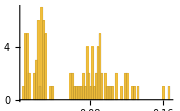
Passed 100/100 (100.%), Time Taken (Min/Med/Mean/Max): (0.007975/0.063349/0.0605241/0.166612)-Graphics-

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};
randomTestInputs=Table[{code20rule, RandomInteger[2^1000], True&}, 100];
DetectPeriodTests[randomTestInputs, False];
```

- - - - - Bad Test Cases - - - - -

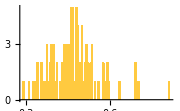
Passed 100/100 (100.%), Time Taken (Min/Med/Mean/Max): (0.29183/0.465963/0.473035/0.811412)-Graphics-

```mathematica
passedTests=0;failedTests=0;badTestInputs={};avgTiming=0;allTimings={};
randomTestInputs=Table[{code1329rule, RandomInteger[3^1000], True&}, 100];
DetectPeriodTests[randomTestInputs, False];
```

## Manual Testing

## Batched